# New Graph Functions in 13.1

## GraphProduct

## Basic Examples

Cartesian product of two graphs:

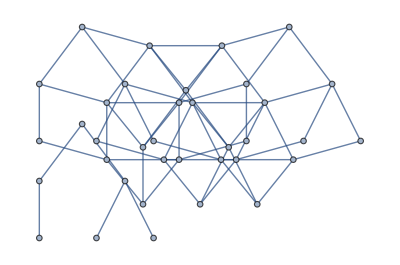

```mathematica
GraphProduct[RandomGraph[{6,5}],RandomGraph[{6,5}]]
```

A table of graph products:

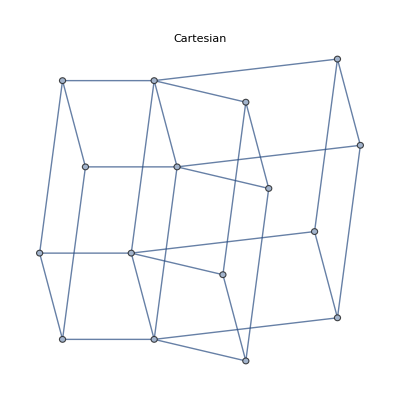
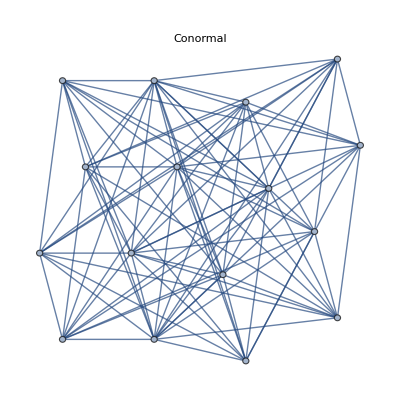
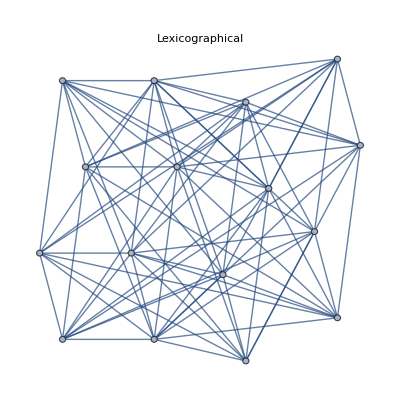
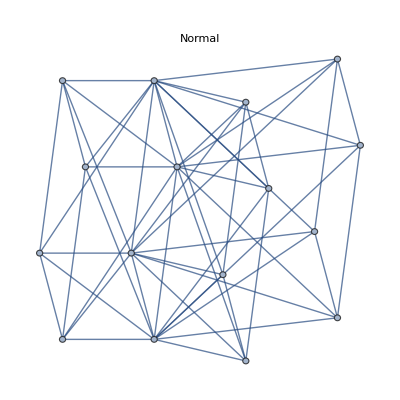
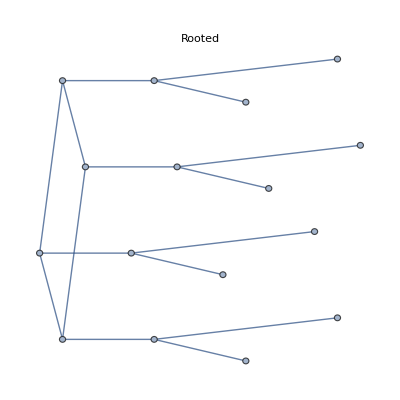
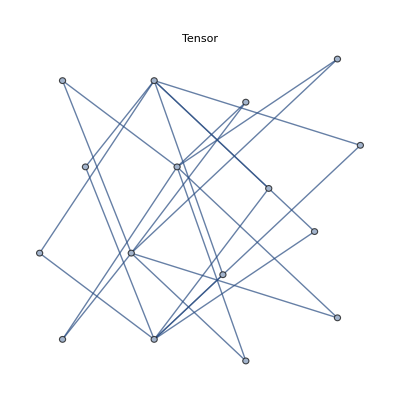

```mathematica
Table[GraphProduct[-Graphics-,-Graphics-,op,],{op,}]
```

Generate grid graphs:

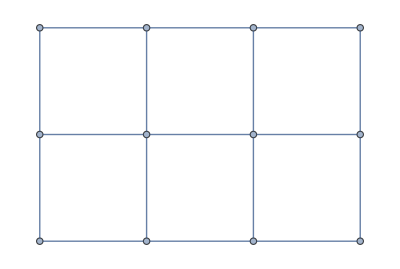

```mathematica
GraphProduct[PathGraph[{1,2,3}],PathGraph[{1,2,3,4}],GraphLayout->"GridEmbedding"]
```

Torus graphs:

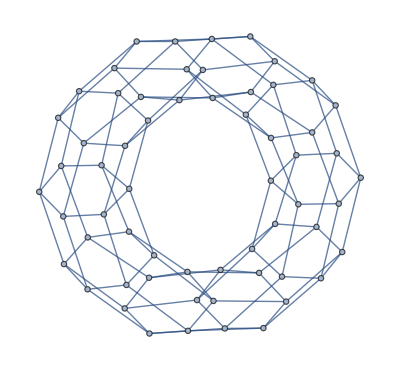

```mathematica
GraphProduct[CycleGraph[10],CycleGraph[6],GraphLayout->"SpringElectricalEmbedding"]
```

## Properties and RElations

For two graphs with v_i vertices, the number of vertices of their product is v_1 v_2:

```mathematica
g=-Graphics-; h=-Graphics-;
```

```mathematica
VertexCount[GraphProduct[g,h]]==VertexCount[g]*VertexCount[h]
```

True

For two undirected graphs with v_i vertices and e_i edges, the number of edge of the Cartesian product is v_1 e_2+v_2 e_1:

```mathematica
g=-Graphics-; h=-Graphics-;
```

```mathematica
{v1,v2}=VertexCount/@{g,h};
```

```mathematica
{e1,e2}=EdgeCount/@{g,h};
```

```mathematica
EdgeCount@GraphProduct[g,h,"Cartesian"]==v1 *e2+v2*e1
```

True

Tensor product is 2 e_1 e_2:

```mathematica
EdgeCount@GraphProduct[g,h,"Tensor"]==2e1 e2
```

True

Lexicographic product is v_1 e_2+e_1 v_2^2:

```mathematica
EdgeCount@GraphProduct[g,h,"Lexicographical"]==v1*e2+e1*v2^2
```

True

Normal product is v_1 e_2+v_2 e_1+2 e_1 e_2:

```mathematica
EdgeCount@GraphProduct[g,h,"Normal"]==v1*e2+v2*e1+2e1 e2
```

True

Co-normal product is v_1^2 e_2+e_1 v_2^2-2 e_1 e_2:

```mathematica
EdgeCount@GraphProduct[g,h,"Conormal"]==v1^2*e2+v2^2*e1-2e1 e2
```

True

Rooted product is v_1 e_2+e_1:

```mathematica
EdgeCount@GraphProduct[g,h,"Rooted"]==v1*e2+e1
```

True

The Cartesian product of two single edges is a cycle:

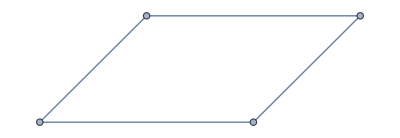

```mathematica
GraphProduct[-Graphics-,-Graphics-, "Cartesian"]
```

The normal product of two single edges is a complete graph:

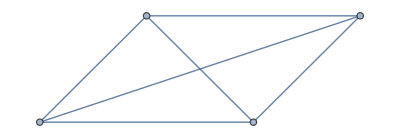

```mathematica
GraphProduct[-Graphics-,-Graphics-, "Normal"]
```

I think my favorite product is the normal product

The tensor product of two single edges is a cross:

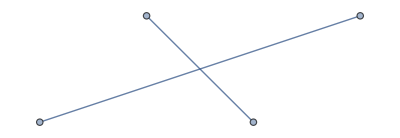

```mathematica
GraphProduct[-Graphics-,-Graphics-, "Tensor"]
```

TorusGraph[{m,n}] is the graph formed from the Cartesian product of the cycle graphs C_n and C_m:

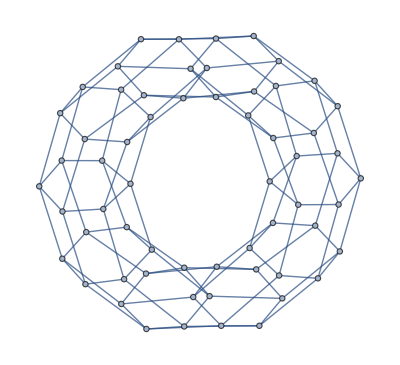

```mathematica
g=TorusGraph[{10,6}]
```

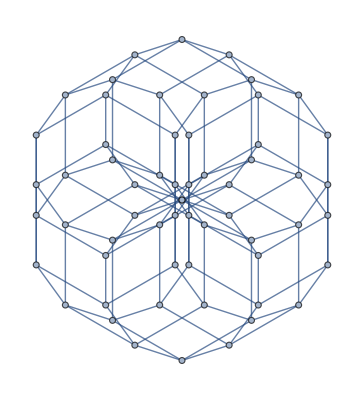

```mathematica
h=GraphProduct[CycleGraph[10],CycleGraph[6]]
```

```mathematica
IsomorphicGraphQ[g,h]
```

True

## GraphJoin

## Basic Examples

Join two graphs:

```mathematica
GraphJoin[-Graphics-,-Graphics-,]
```

-Graphics-

Plot the structure of the adjacency matrices:

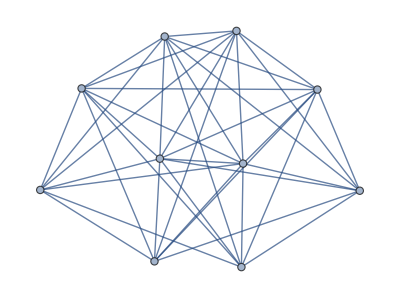
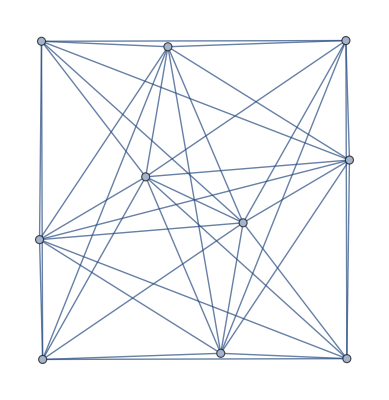
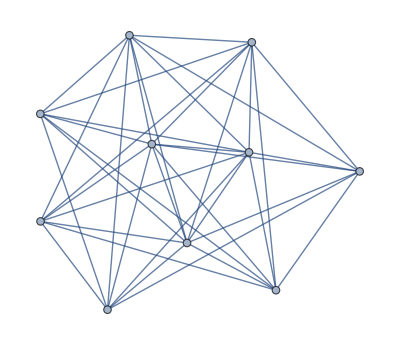

```mathematica
GraphJoin@@@Table[RandomGraph[{5,7}],3,2]
```

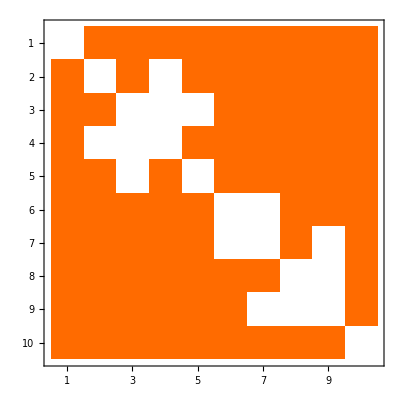
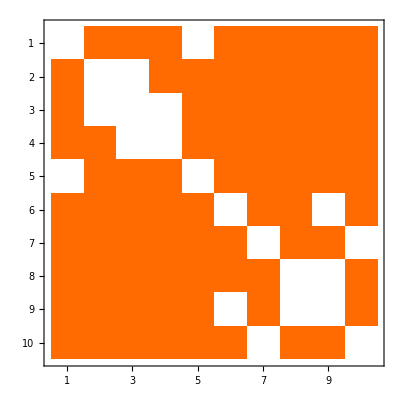
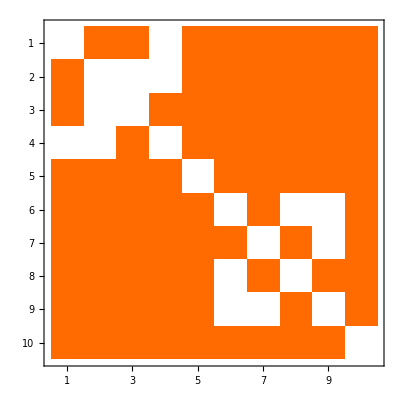

```mathematica
Map[MatrixPlot@*AdjacencyMatrix,GraphJoin@@@Table[RandomGraph[{5,7}],3,2]]
```

Generate wheel graphs:

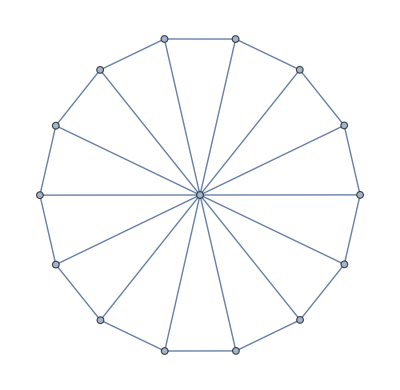

```mathematica
GraphJoin[Graph[{1},{}],CycleGraph[14]]
```

Complete graphs K_(3,4):

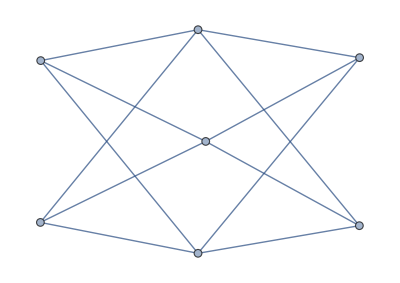

```mathematica
GraphJoin[Graph[Range[3],{}],Graph[Range[4],{}]]
```

Generate dipyramid graphs:

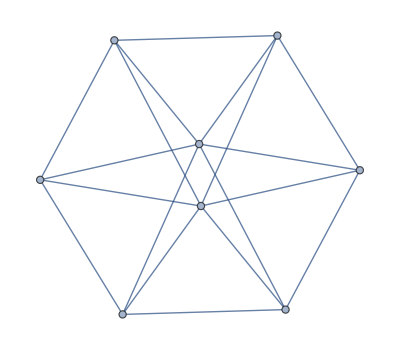

```mathematica
GraphJoin[Graph[{1,2},{}],CycleGraph[6]]
```

## GraphSum

## Basic Examples

Sum of two graphs:

```mathematica
GraphSum[-Graphics-,   -Graphics-   ,]
```

-Graphics-

Generate complete graphs:

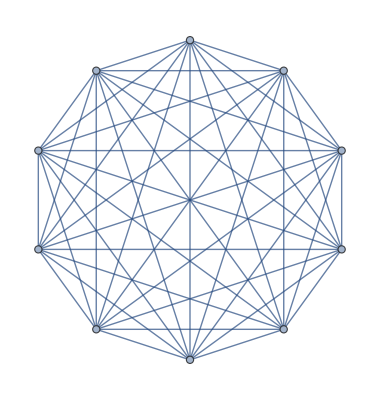

```mathematica
GraphSum[g=RandomGraph[{10,7}],GraphComplement[g]]
```

Graphs with parallel edges:

```mathematica
GraphSum[g=RandomGraph[{10,18}],g]
```

-Graphics-

## Properties and Relations

The sum of any graph and its complement is a CompleteGraph:

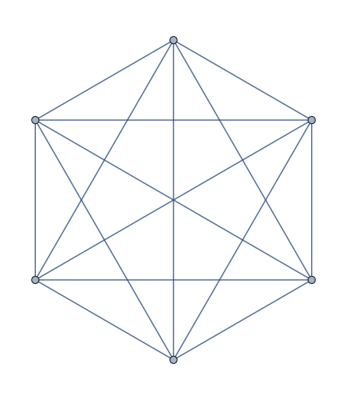

```mathematica
GraphSum[g=CycleGraph[6],GraphComplement[g]]
```

```mathematica
CompleteGraphQ[GraphSum[g=CycleGraph[6],GraphComplement[g]]]
```

True

The sum of any graph and itself is a multigraph:

```mathematica
GraphSum[g=RandomGraph[{5,7}],g]
```

-Graphics-

The sum of graphs can be obtained by joining the edges of the graphs:

```mathematica
g=GridGraph[{2,3}];
h=CycleGraph[3];
{GraphSum[g,h],Graph[Join[EdgeList[g],EdgeList[h]]]}
```

{-Graphics-,-Graphics-}

The sum of graphs can be obtained by adding their adjacency matrices together:


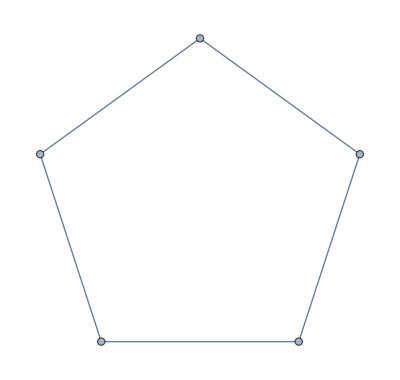

```mathematica
{g=CompleteGraph[5],h=CycleGraph[5]}
```

```mathematica
{GraphSum[g,h],AdjacencyGraph[Plus[AdjacencyMatrix[g]+AdjacencyMatrix[h]]]}
```

{-Graphics-,-Graphics-}

GraphSum gives the same result as GraphUnion if graphs have different vertex names:

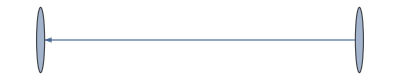
{-Graphics-,-Graphics-}

```mathematica
{g=Graph[{a->b}],h=Graph[{1->2}]}
```

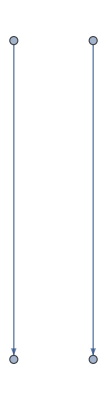
{-Graphics-,-Graphics-}

```mathematica
{GraphSum[g,h],GraphUnion[g,h]}
```

## Neat Examples

```mathematica
Subgraph[g=GraphSum[g=RandomGraph[{100,200}],g,g,g,g],First@ConnectedComponents[g]]
```

-Graphics-

## TorusGraph

## Basic Examples

The first few torus graphs:

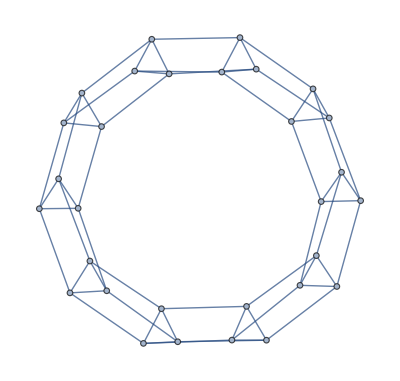
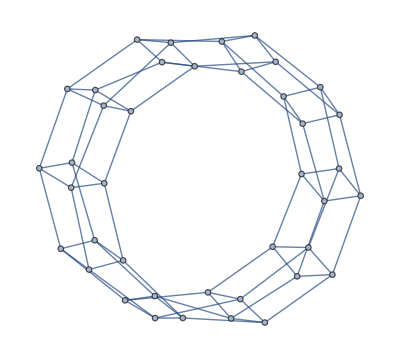
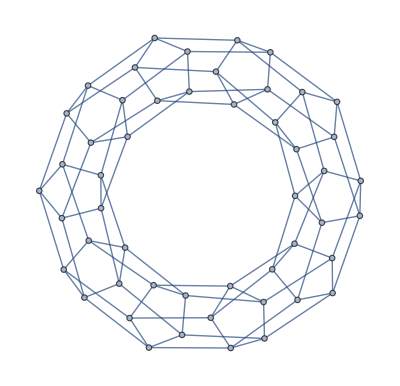
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[TorusGraph[{10,i}],{i,3,6}]
```

Higher-dimensional torus graphs:

```mathematica
{TorusGraph[{10,2,2}],TorusGraph[{10,2,2,2}]}
```

{-Graphics-,-Graphics-}

Directed torus graphs:

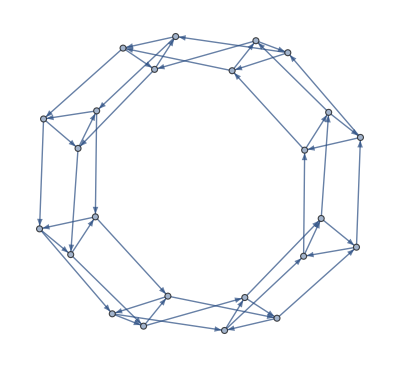
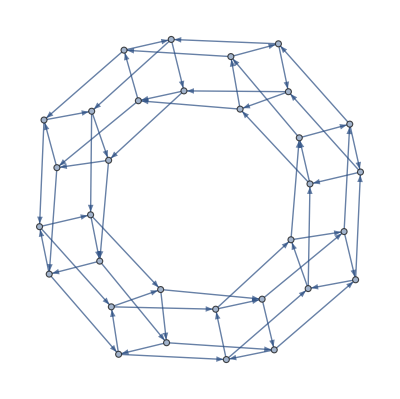
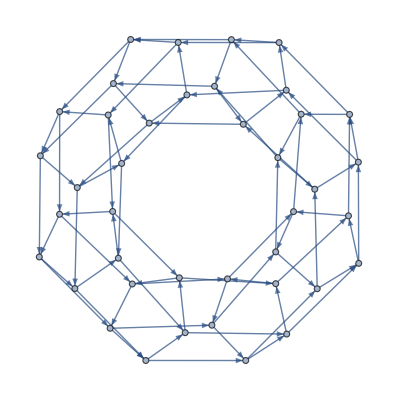
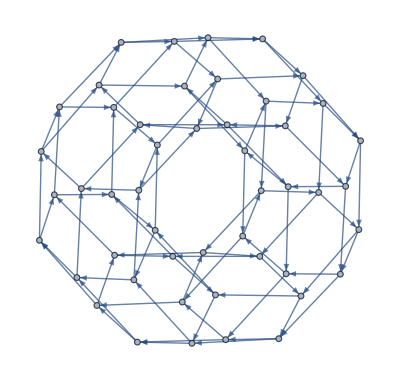

```mathematica
Table[TorusGraph[{8,i},DirectedEdges->True],{i,3,6}]
```

## BuckyballGraph

## BasicExamples

The buckyball graph:

```mathematica
BuckyballGraph[]
```

-Graphics3D-

Generate a class I, order-3 buckyball graph:

```mathematica
BuckyballGraph[3,"I"]
```

-Graphics3D-

A class II, order-3 buckyball graph:

```mathematica
BuckyballGraph[3,"II"]
```

-Graphics3D-

```mathematica
Table[BuckyballGraph[0,VertexShapeFunction->vf,VertexSize->0.3,PlotLabel->vf],{vf,{"DownTrapezoid","UpTrapezoid","Parallelogram","FiveDown","Circle","Cuboid","Star","Capsule"}}]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}